```mathematica
ClearAll[Evaluate[Context[]<>"*"]];
ClearSystemCache[];
```

```mathematica
(* now I need to multiply outside by fkμ/2 -> k/2 only. The μ is already accounted for... *)
```

### Cosmological Parameters (online CAMB)

```mathematica
c=3 10^8 ;
A=2.10732 10^-9;
Δϕ=9/25 A;
h=0.677;
Ωch2=0.11923;
Ωbh2=(*0.001×*)0.02247;
ns=0.96824;

H0=100h 1000;

fNL=1000;
NGparam=1944/625 π^4 A^2 fNL;
```

```mathematica
Ωb=Ωbh2/h^2;Ωc=Ωch2/h^2;Ωm=Ωb+Ωc;
```

### Linear Power Spectrum

#### Eisenstein & Hu Fitting Function

```mathematica
TransferFunction[h0_,Ωb0_,Ωc0_,Ω00_]:=Module[
{h=h0,Ωb=Ωb0,Ωc=Ωc0,Ω0=Ω00,H0,Θ,zeq,keq,kSilk,qq,a1,a2,αc,b1,b2,βc,zd,B1,B2,R,Rd,Req,s,G,αb,f,C1,C2,Tt0kαcβc,Tt0k1βc,Tt0k11,Tc,βnode,βb,st,Tb,T,AG,Gama,qu,Co,Lo,To},
H0=100000 h/299792458;
Θ=2.728/2.7;
zeq=25000Ω0 h^2 Θ^-4;
keq=Sqrt[2Ω0 H0^2 zeq];
kSilk=1.6(Ωb h^2)^0.52 (Ω0 h^2)^0.73 (1+(10.4 Ω0 h^2)^-0.95);
qq=kk Θ^2 (Ω0 h^2)^-1;
a1=(46.9Ω0 h^2)^0.670 (1+(32.1Ω0 h^2)^-0.532);
a2=(12.0Ω0 h^2)^0.424 (1+(45.0Ω0 h^2)^-0.582);
αc=a1^(-Ωb/Ω0) a2^-(Ωb/Ω0)^3;
b1=0.944(1+(458Ω0 h^2)^-0.708)^-1;
b2=(0.395Ω0 h^2)^-0.0266;
βc=(1+b1 ((Ωc/Ω0)^b2-1))^-1;
zd=1291(Ω0 h^2)^0.251/(1+0.659(Ω0 h^2)^0.828) (1+B1 (Ωb h^2)^B2);
B1=0.313(Ω0 h^2)^-0.419 (1+0.607(Ω0 h^2)^0.674);
B2=0.238(Ω0 h^2)^0.223;
R=31.5Ωb h^2 Θ^-4 (z/1000)^-1;
Rd=ReplaceAll[R,z->zd];
Req=ReplaceAll[R,z->zeq];
s=2/(3keq) Sqrt[6/Req]Log[(Sqrt[1+Rd]+Sqrt[Rd+Req])/(1+Sqrt[Req])];
G=y (-6Sqrt[1+y]+(2+3y)Log[(Sqrt[1+y]+1)/(Sqrt[1+y]-1)]);
αb=2.07 keq s (1+Rd)^(-3/4) ReplaceAll[G,y->(1+zeq)/(1+zd)];
f=1/(1+(kk s/5.4)^4);
C1=14.2/αc+386/(1+69.9qq^1.08);
C2=14.2+386/(1+69.9qq^1.08);
Tt0kαcβc=Log[E+1.8βc qq]/(Log[E+1.8βc qq]+C1 qq^2);
Tt0k1βc=Log[E+1.8βc qq]/(Log[E+1.8βc qq]+C2 qq^2);
Tt0k11=Log[E+1.8qq]/(Log[E+1.8qq]+C2 qq^2);
Tc=f Tt0k1βc+(1-f)Tt0kαcβc;
βnode=8.41(Ω0 h^2)^0.435;
βb=0.5+Ωb/Ω0+(3-2Ωb/Ω0)Sqrt[(17.2Ω0 h^2)^2+1];
st=s/(1+(βnode/kk/s)^3)^(1/3);
Tb=(Tt0k11/(1+(kk s/5.2)^2)+αb/(1+(βb/kk /s)^3) E^-(kk/kSilk)^1.4)Sin[kk st]/(kk st);
T=Ωb/Ω0 Tb+Ωc/Ω0 Tc;
AG=1-0.328*Log[431*Ω0*h^2]*(Ωb/Ω0)+0.38*Log[22.3*Ω0*h^2]*(Ωb/Ω0)^2;
Gama=Ω0*h*(AG+(1-AG)/(1+(0.43*kk*s)^4));
qu=kk/h*Θ^2/Gama;
Co=14.2+731.0/(1+62.5*qu);
Lo=Log[2*E+1.8*qu];
To=Lo/(Lo+Co*qu^2);
{T,Tc,To}
]
```

```mathematica
(* Smooth part *)
Tc[x_]=(TransferFunction[h,Ωb,Ωc,Ωm]/.{kk->x h})⟦3⟧;
(* The full transfer function including wiggles *)
Tcw[x_]=(TransferFunction[h,Ωb,Ωc,Ωm]/.{kk->x h})⟦1⟧;
```

```mathematica
(* Define the thransfer funciton in terms of physical densities and comoving k *)
T[x_,ωcdm_,ωb_,h_,ns_]:=((TransferFunction[h,ωb/h^2,ωcdm/h^2,(ωb+ωcdm)/h^2](kk/0.05)^((ns-1)/2))/.{kk->x h})⟦1⟧;
```

#### Growth Factor

```mathematica
(* Analytic solution for the growth factor in LCDM. *)
replace=DSolve[{a^2 y''[a]+3a y'[a]-3/2 1/(1+(1/Ωmm-1)a^3)a y'[a]-3/2 1/(1+(1/Ωmm-1)a^3)y[a]==0},y[a],a];
```

```mathematica
(* Expand in a around a=0 to fix constants C[1] and C[2]. We know that at early times D[0]=0 and D'[0]=1. *)
Series[((y[a]/.replace)⟦1⟧)//Simplify,{a,0,2}]//FullSimplify
```

(√-Ωmm C[1])/a^(3/2)-(2 C[2] a)/(5 Ωmm)+((-1+Ωmm) C[1] a^(3/2))/(2 √-Ωmm)+O[a]^(5/2)

```mathematica
(* Define the growth factor in terms of all relevant cosmological parameters. *)
D1[ωcdm_,ωb_,h_,z_]:=(((y[a]/.replace)⟦1⟧)/.{C[1]->0,C[2]->-5(ωcdm+ωb)/(2 h^2)})/.{Ωmm->(ωcdm+ωb)/h^2,a->1/(1+z)};
```

#### Constructing the Power Spectrum

```mathematica
Mm[k_,ωcdm_,ωb_,h_,ns_]:=k^2 T[k,ωcdm,ωb,h,ns];
Hh0=(100*1000)/c;
(******)
(*cut=0.1;*)
(******)
PlinEH[k_,z_,ωcdm_,ωb_,h_,As_,ns_,b1_]:=b1^2(2/5(h^2 D1[ωcdm,ωb,h,z])/((ωb+ωcdm) Hh0^2))^2(2 π^2 As)Mm[k,ωcdm,ωb,h,ns]^2 1/k^3(*ⅇ^(-(k/cut)^2)*);
ℳ[k_,z_,ωcdm_,ωb_,h_]:=(2/5(h^2 D1[ωcdm,ωb,h,z])/((ωb+ωcdm) Hh0^2))Mm[k,ωcdm,ωb,h,1];
Pℳ[k_,z_,ωcdm_,ωb_,h_]:=ℳ[k,z,ωcdm,ωb,h]/k^2;
```

```mathematica
Pℳhelp[k_]=Pℳ[k,0,Ωch2,Ωbh2,h];
```

### Decomposition into power laws

```mathematica
kBins[Nmax_,kmin_,kmax_]:=Module[{Δ,result},
Δ=1/(Nmax(*-1*))Log[kmax/kmin]//N;
result=Table[kmin Exp[(i-1) Δ],{i,1,Nmax}];
result
];
```

```mathematica
CoeffPow[b_,Nmax_,kmin_,kmax_,Pk_]:=Module[{Δ,n,m,kn,ηm,ηn,Pn,cn,cnsym,result},
Δ=1/(Nmax(*-1*))Log[kmax/kmin]//N;
kn=Table[kmin Exp[(i-1) Δ],{i,1,Nmax}];
ηm=Table[b+(2π I)/(Nmax Δ)(j-Nmax/2-1),{j,1,Nmax+1}];

Pn=Table[Pk[kn⟦i⟧]Exp[-b(i-1)Δ],{i,1,Nmax}];
cn=Fourier[Pn,FourierParameters->{-1,-1}];
cnsym=Table[If[(j-Nmax/2)<1,kmin^(-ηm⟦j⟧)Conjugate[cn⟦-j+Nmax/2+2(*,1*)⟧],kmin^(-ηm⟦j⟧)cn⟦j-Nmax/2(*,1*)⟧],{j,1,Nmax+1}];
(*cnsym⟦1⟧=cnsym⟦1⟧/2;
cnsym⟦Length[cnsym]⟧=cnsym⟦Length[cnsym]⟧/2;*)
result=Table[{cnsym⟦i⟧,ηm⟦i⟧},{i,1,Length[ηm]}];
result
];
```

### PT kernels

```mathematica
perm12=Permutations[{q1,q2}];
perm123=Permutations[{q1,q2,q3}];
```

```mathematica
Clear[Fn,Gn,n,m];
Fn[n_,v_]=If[n==1,1,Sum[Gn[m,v[[1;;m]]]/((2n+3)(n-1))((2n+1)al[Total[v[[1;;m]]],Total[v[[m+1;;n]]]]Fn[n-m,v[[m+1;;n]]]+2be[Total[v[[1;;m]]],Total[v[[m+1;;n]]]]Gn[n-m,v[[m+1;;n]]]),{m,1,n-1}]];
Gn[n_,v_]=If[n==1,1,Sum[Gn[m,v[[1;;m]]]/((2n+3)(n-1))(3al[Total[v[[1;;m]]],Total[v[[m+1;;n]]]]Fn[n-m,v[[m+1;;n]]]+2n be[Total[v[[1;;m]]],Total[v[[m+1;;n]]]]Gn[n-m,v[[m+1;;n]]]),{m,1,n-1}]];
```

```mathematica
F2s[q1_,q2_]=Simplify[Sum[1/Length[perm12]Fn[2,{perm12[[i,1]],perm12[[i,2]]}],{i,1,Length[perm12]}]];
F3s[q1_,q2_,q3_]=Simplify[Sum[1/Length[perm123]Fn[3,{perm123[[i,1]],perm123[[i,2]],perm123[[i,3]]}],{i,1,Length[perm123]}]];
```

```mathematica
G2s[q1_,q2_]=Simplify[Sum[1/Length[perm12]Gn[2,{perm12[[i,1]],perm12[[i,2]]}],{i,1,Length[perm12]}]];
```

```mathematica
alf[k1_,k2_]=(k1+k2).k1/(k1.k1);
bef[k1_,k2_]=(k1+k2).(k1+k2)(k1.k2)/2/(k1.k1)/(k2.k2) ;
alfm[k1_,k2_]=1+1/2(mag[k1+k2]^2-mag[k1]^2-mag[k2]^2)/mag[k1]^2;
befm[k1_,k2_]=(mag[k1+k2]^2(mag[k1+k2]^2-mag[k1]^2-mag[k2]^2))/(4 mag[k1]^2 mag[k2]^2);
sigma2[k1_,k2_]=1/4((mag[k1+k2]^2-mag[k1]^2-mag[k2]^2)^2)/(mag[k1]^2 mag[k2]^2)-1;
```

```mathematica
(* NG shape *)
```

```mathematica
Northo=(840 π^2-7363-189(20 π^2-193))/(29114-2940 π^2);
p=27/(743/(7(20 π^2-193))-21);
kT=mag[k1]+mag[k2]+mag[k3];
e2=mag[k1]mag[k2]+mag[k2]mag[k3]+mag[k3]mag[k1];
e3=mag[k1]mag[k2]mag[k3];
Δ=(kT-2mag[k1])(kT-2mag[k2])(kT-2mag[k3]);
Γ=2/3 e2-1/3(mag[k1]^2+mag[k2]^2+mag[k3]^2);
```

```mathematica
𝒮[k1_,k2_,k3_]=Simplify[1/Northo((1+p)Δ/e3-p Γ^3/e3^2)]
```

(-((-7363+840 π^2) mag[k1] mag[k2] (mag[k1]-mag[k2]-mag[k3]) (mag[k1]+mag[k2]-mag[k3]) mag[k3] (mag[k1]-mag[k2]+mag[k3]))+7 (-193+20 π^2) (mag[k1]^2+(mag[k2]-mag[k3])^2-2 mag[k1] (mag[k2]+mag[k3]))^3)/((29114-2940 π^2) mag[k1]^2 mag[k2]^2 mag[k3]^2)

### Low-k brute force

```mathematica
integrand1=(2 1/mag[q] 𝒮[q,k-q,k]/.{al->alfm,be->befm})/.{mag[0]->0,mag[-q]->q,mag[q]->q,mag[k]->k,mag[k-q]->kmq,mag[k+q]->kmq}//Expand
```

17698/(k (29114-2940 π^2))+(54040 k)/(kmq^2 (29114-2940 π^2))+17698/(kmq (29114-2940 π^2))+(54040 kmq)/(k^2 (29114-2940 π^2))-(1680 π^2)/(k (29114-2940 π^2))-(5600 k π^2)/(kmq^2 (29114-2940 π^2))-(1680 π^2)/(kmq (29114-2940 π^2))-(5600 kmq π^2)/(k^2 (29114-2940 π^2))-(40530 k^2)/((29114-2940 π^2) q^3)-(2702 k^4)/(kmq^2 (29114-2940 π^2) q^3)+(16212 k^3)/(kmq (29114-2940 π^2) q^3)+(54040 k kmq)/((29114-2940 π^2) q^3)-(40530 kmq^2)/((29114-2940 π^2) q^3)+(16212 kmq^3)/(k (29114-2940 π^2) q^3)-(2702 kmq^4)/(k^2 (29114-2940 π^2) q^3)+(4200 k^2 π^2)/((29114-2940 π^2) q^3)+(280 k^4 π^2)/(kmq^2 (29114-2940 π^2) q^3)-(1680 k^3 π^2)/(kmq (29114-2940 π^2) q^3)-(5600 k kmq π^2)/((29114-2940 π^2) q^3)+(4200 kmq^2 π^2)/((29114-2940 π^2) q^3)-(1680 kmq^3 π^2)/(k (29114-2940 π^2) q^3)+(280 kmq^4 π^2)/(k^2 (29114-2940 π^2) q^3)+(17698 k)/((29114-2940 π^2) q^2)+(16212 k^3)/(kmq^2 (29114-2940 π^2) q^2)-(33910 k^2)/(kmq (29114-2940 π^2) q^2)+(17698 kmq)/((29114-2940 π^2) q^2)-(33910 kmq^2)/(k (29114-2940 π^2) q^2)+(16212 kmq^3)/(k^2 (29114-2940 π^2) q^2)-(1680 k π^2)/((29114-2940 π^2) q^2)-(1680 k^3 π^2)/(kmq^2 (29114-2940 π^2) q^2)+(3360 k^2 π^2)/(kmq (29114-2940 π^2) q^2)-(1680 kmq π^2)/((29114-2940 π^2) q^2)+(3360 kmq^2 π^2)/(k (29114-2940 π^2) q^2)-(1680 kmq^3 π^2)/(k^2 (29114-2940 π^2) q^2)+45664/((29114-2940 π^2) q)-(40530 k^2)/(kmq^2 (29114-2940 π^2) q)+(17698 k)/(kmq (29114-2940 π^2) q)+(17698 kmq)/(k (29114-2940 π^2) q)-(40530 kmq^2)/(k^2 (29114-2940 π^2) q)-(5040 π^2)/((29114-2940 π^2) q)+(4200 k^2 π^2)/(kmq^2 (29114-2940 π^2) q)-(1680 k π^2)/(kmq (29114-2940 π^2) q)-(1680 kmq π^2)/(k (29114-2940 π^2) q)+(4200 kmq^2 π^2)/(k^2 (29114-2940 π^2) q)-(40530 q)/(k^2 (29114-2940 π^2))-(40530 q)/(kmq^2 (29114-2940 π^2))-(33910 q)/(k kmq (29114-2940 π^2))+(4200 π^2 q)/(k^2 (29114-2940 π^2))+(4200 π^2 q)/(kmq^2 (29114-2940 π^2))+(3360 π^2 q)/(k kmq (29114-2940 π^2))+(16212 q^2)/(k kmq^2 (29114-2940 π^2))+(16212 q^2)/(k^2 kmq (29114-2940 π^2))-(1680 π^2 q^2)/(k kmq^2 (29114-2940 π^2))-(1680 π^2 q^2)/(k^2 kmq (29114-2940 π^2))-(2702 q^3)/(k^2 kmq^2 (29114-2940 π^2))+(280 π^2 q^3)/(k^2 kmq^2 (29114-2940 π^2))

```mathematica
integrand1=μ(integrand1/.{kmq->Sqrt[k^2+q^2-2 q k μ]});
```

```mathematica
integrand2=(2 1/mag[k-q]^2 𝒮[q,k-q,k]/.{al->alfm,be->befm})/.{mag[0]->0,mag[-q]->q,mag[q]->q,mag[k]->k,mag[k-q]->kmq,mag[k+q]->kmq}//Expand
```

-40530/(k^2 (29114-2940 π^2))-(40530 k^2)/(kmq^4 (29114-2940 π^2))+(17698 k)/(kmq^3 (29114-2940 π^2))+45664/(kmq^2 (29114-2940 π^2))+17698/(k kmq (29114-2940 π^2))+(4200 π^2)/(k^2 (29114-2940 π^2))+(4200 k^2 π^2)/(kmq^4 (29114-2940 π^2))-(1680 k π^2)/(kmq^3 (29114-2940 π^2))-(5040 π^2)/(kmq^2 (29114-2940 π^2))-(1680 π^2)/(k kmq (29114-2940 π^2))-40530/((29114-2940 π^2) q^2)-(2702 k^4)/(kmq^4 (29114-2940 π^2) q^2)+(16212 k^3)/(kmq^3 (29114-2940 π^2) q^2)-(40530 k^2)/(kmq^2 (29114-2940 π^2) q^2)+(54040 k)/(kmq (29114-2940 π^2) q^2)+(16212 kmq)/(k (29114-2940 π^2) q^2)-(2702 kmq^2)/(k^2 (29114-2940 π^2) q^2)+(4200 π^2)/((29114-2940 π^2) q^2)+(280 k^4 π^2)/(kmq^4 (29114-2940 π^2) q^2)-(1680 k^3 π^2)/(kmq^3 (29114-2940 π^2) q^2)+(4200 k^2 π^2)/(kmq^2 (29114-2940 π^2) q^2)-(5600 k π^2)/(kmq (29114-2940 π^2) q^2)-(1680 kmq π^2)/(k (29114-2940 π^2) q^2)+(280 kmq^2 π^2)/(k^2 (29114-2940 π^2) q^2)-33910/(k (29114-2940 π^2) q)+(16212 k^3)/(kmq^4 (29114-2940 π^2) q)-(33910 k^2)/(kmq^3 (29114-2940 π^2) q)+(17698 k)/(kmq^2 (29114-2940 π^2) q)+17698/(kmq (29114-2940 π^2) q)+(16212 kmq)/(k^2 (29114-2940 π^2) q)+(3360 π^2)/(k (29114-2940 π^2) q)-(1680 k^3 π^2)/(kmq^4 (29114-2940 π^2) q)+(3360 k^2 π^2)/(kmq^3 (29114-2940 π^2) q)-(1680 k π^2)/(kmq^2 (29114-2940 π^2) q)-(1680 π^2)/(kmq (29114-2940 π^2) q)-(1680 kmq π^2)/(k^2 (29114-2940 π^2) q)+(54040 k q)/(kmq^4 (29114-2940 π^2))+(17698 q)/(kmq^3 (29114-2940 π^2))+(17698 q)/(k kmq^2 (29114-2940 π^2))+(54040 q)/(k^2 kmq (29114-2940 π^2))-(5600 k π^2 q)/(kmq^4 (29114-2940 π^2))-(1680 π^2 q)/(kmq^3 (29114-2940 π^2))-(1680 π^2 q)/(k kmq^2 (29114-2940 π^2))-(5600 π^2 q)/(k^2 kmq (29114-2940 π^2))-(40530 q^2)/(kmq^4 (29114-2940 π^2))-(33910 q^2)/(k kmq^3 (29114-2940 π^2))-(40530 q^2)/(k^2 kmq^2 (29114-2940 π^2))+(4200 π^2 q^2)/(kmq^4 (29114-2940 π^2))+(3360 π^2 q^2)/(k kmq^3 (29114-2940 π^2))+(4200 π^2 q^2)/(k^2 kmq^2 (29114-2940 π^2))+(16212 q^3)/(k kmq^4 (29114-2940 π^2))+(16212 q^3)/(k^2 kmq^3 (29114-2940 π^2))-(1680 π^2 q^3)/(k kmq^4 (29114-2940 π^2))-(1680 π^2 q^3)/(k^2 kmq^3 (29114-2940 π^2))-(2702 q^4)/(k^2 kmq^4 (29114-2940 π^2))+(280 π^2 q^4)/(k^2 kmq^4 (29114-2940 π^2))

```mathematica
integrand2=k(integrand2/.{kmq->Sqrt[k^2+q^2-2 q k μ]});
```

```mathematica
integrand3=(2 q/mag[k-q]^2 𝒮[q,k-q,k]/.{al->alfm,be->befm})/.{mag[0]->0,mag[-q]->q,mag[q]->q,mag[k]->k,mag[k-q]->kmq,mag[k+q]->kmq}//Expand
```

-33910/(k (29114-2940 π^2))+(16212 k^3)/(kmq^4 (29114-2940 π^2))-(33910 k^2)/(kmq^3 (29114-2940 π^2))+(17698 k)/(kmq^2 (29114-2940 π^2))+17698/(kmq (29114-2940 π^2))+(16212 kmq)/(k^2 (29114-2940 π^2))+(3360 π^2)/(k (29114-2940 π^2))-(1680 k^3 π^2)/(kmq^4 (29114-2940 π^2))+(3360 k^2 π^2)/(kmq^3 (29114-2940 π^2))-(1680 k π^2)/(kmq^2 (29114-2940 π^2))-(1680 π^2)/(kmq (29114-2940 π^2))-(1680 kmq π^2)/(k^2 (29114-2940 π^2))-40530/((29114-2940 π^2) q)-(2702 k^4)/(kmq^4 (29114-2940 π^2) q)+(16212 k^3)/(kmq^3 (29114-2940 π^2) q)-(40530 k^2)/(kmq^2 (29114-2940 π^2) q)+(54040 k)/(kmq (29114-2940 π^2) q)+(16212 kmq)/(k (29114-2940 π^2) q)-(2702 kmq^2)/(k^2 (29114-2940 π^2) q)+(4200 π^2)/((29114-2940 π^2) q)+(280 k^4 π^2)/(kmq^4 (29114-2940 π^2) q)-(1680 k^3 π^2)/(kmq^3 (29114-2940 π^2) q)+(4200 k^2 π^2)/(kmq^2 (29114-2940 π^2) q)-(5600 k π^2)/(kmq (29114-2940 π^2) q)-(1680 kmq π^2)/(k (29114-2940 π^2) q)+(280 kmq^2 π^2)/(k^2 (29114-2940 π^2) q)-(40530 q)/(k^2 (29114-2940 π^2))-(40530 k^2 q)/(kmq^4 (29114-2940 π^2))+(17698 k q)/(kmq^3 (29114-2940 π^2))+(45664 q)/(kmq^2 (29114-2940 π^2))+(17698 q)/(k kmq (29114-2940 π^2))+(4200 π^2 q)/(k^2 (29114-2940 π^2))+(4200 k^2 π^2 q)/(kmq^4 (29114-2940 π^2))-(1680 k π^2 q)/(kmq^3 (29114-2940 π^2))-(5040 π^2 q)/(kmq^2 (29114-2940 π^2))-(1680 π^2 q)/(k kmq (29114-2940 π^2))+(54040 k q^2)/(kmq^4 (29114-2940 π^2))+(17698 q^2)/(kmq^3 (29114-2940 π^2))+(17698 q^2)/(k kmq^2 (29114-2940 π^2))+(54040 q^2)/(k^2 kmq (29114-2940 π^2))-(5600 k π^2 q^2)/(kmq^4 (29114-2940 π^2))-(1680 π^2 q^2)/(kmq^3 (29114-2940 π^2))-(1680 π^2 q^2)/(k kmq^2 (29114-2940 π^2))-(5600 π^2 q^2)/(k^2 kmq (29114-2940 π^2))-(40530 q^3)/(kmq^4 (29114-2940 π^2))-(33910 q^3)/(k kmq^3 (29114-2940 π^2))-(40530 q^3)/(k^2 kmq^2 (29114-2940 π^2))+(4200 π^2 q^3)/(kmq^4 (29114-2940 π^2))+(3360 π^2 q^3)/(k kmq^3 (29114-2940 π^2))+(4200 π^2 q^3)/(k^2 kmq^2 (29114-2940 π^2))+(16212 q^4)/(k kmq^4 (29114-2940 π^2))+(16212 q^4)/(k^2 kmq^3 (29114-2940 π^2))-(1680 π^2 q^4)/(k kmq^4 (29114-2940 π^2))-(1680 π^2 q^4)/(k^2 kmq^3 (29114-2940 π^2))-(2702 q^5)/(k^2 kmq^4 (29114-2940 π^2))+(280 π^2 q^5)/(k^2 kmq^4 (29114-2940 π^2))

```mathematica
integrand3=-μ(integrand3/.{kmq->Sqrt[k^2+q^2-2 q k μ]});
```

```mathematica
integrandqμ[k_,q_,μ_]=(integrand1+integrand2+integrand3)
```

k (-40530/(k^2 (29114-2940 π^2))+(4200 π^2)/(k^2 (29114-2940 π^2))-40530/((29114-2940 π^2) q^2)+(4200 π^2)/((29114-2940 π^2) q^2)-33910/(k (29114-2940 π^2) q)+(3360 π^2)/(k (29114-2940 π^2) q)-(40530 k^2)/((29114-2940 π^2) (k^2+q^2-2 k q μ)^2)+(4200 k^2 π^2)/((29114-2940 π^2) (k^2+q^2-2 k q μ)^2)-(2702 k^4)/((29114-2940 π^2) q^2 (k^2+q^2-2 k q μ)^2)+(280 k^4 π^2)/((29114-2940 π^2) q^2 (k^2+q^2-2 k q μ)^2)+(16212 k^3)/((29114-2940 π^2) q (k^2+q^2-2 k q μ)^2)-(1680 k^3 π^2)/((29114-2940 π^2) q (k^2+q^2-2 k q μ)^2)+(54040 k q)/((29114-2940 π^2) (k^2+q^2-2 k q μ)^2)-(5600 k π^2 q)/((29114-2940 π^2) (k^2+q^2-2 k q μ)^2)-(40530 q^2)/((29114-2940 π^2) (k^2+q^2-2 k q μ)^2)+(4200 π^2 q^2)/((29114-2940 π^2) (k^2+q^2-2 k q μ)^2)+(16212 q^3)/(k (29114-2940 π^2) (k^2+q^2-2 k q μ)^2)-(1680 π^2 q^3)/(k (29114-2940 π^2) (k^2+q^2-2 k q μ)^2)-(2702 q^4)/(k^2 (29114-2940 π^2) (k^2+q^2-2 k q μ)^2)+(280 π^2 q^4)/(k^2 (29114-2940 π^2) (k^2+q^2-2 k q μ)^2)+(17698 k)/((29114-2940 π^2) (k^2+q^2-2 k q μ)^(3/2))-(1680 k π^2)/((29114-2940 π^2) (k^2+q^2-2 k q μ)^(3/2))+(16212 k^3)/((29114-2940 π^2) q^2 (k^2+q^2-2 k q μ)^(3/2))-(1680 k^3 π^2)/((29114-2940 π^2) q^2 (k^2+q^2-2 k q μ)^(3/2))-(33910 k^2)/((29114-2940 π^2) q (k^2+q^2-2 k q μ)^(3/2))+(3360 k^2 π^2)/((29114-2940 π^2) q (k^2+q^2-2 k q μ)^(3/2))+(17698 q)/((29114-2940 π^2) (k^2+q^2-2 k q μ)^(3/2))-(1680 π^2 q)/((29114-2940 π^2) (k^2+q^2-2 k q μ)^(3/2))-(33910 q^2)/(k (29114-2940 π^2) (k^2+q^2-2 k q μ)^(3/2))+(3360 π^2 q^2)/(k (29114-2940 π^2) (k^2+q^2-2 k q μ)^(3/2))+(16212 q^3)/(k^2 (29114-2940 π^2) (k^2+q^2-2 k q μ)^(3/2))-(1680 π^2 q^3)/(k^2 (29114-2940 π^2) (k^2+q^2-2 k q μ)^(3/2))+45664/((29114-2940 π^2) (k^2+q^2-2 k q μ))-(5040 π^2)/((29114-2940 π^2) (k^2+q^2-2 k q μ))-(40530 k^2)/((29114-2940 π^2) q^2 (k^2+q^2-2 k q μ))+(4200 k^2 π^2)/((29114-2940 π^2) q^2 (k^2+q^2-2 k q μ))+(17698 k)/((29114-2940 π^2) q (k^2+q^2-2 k q μ))-(1680 k π^2)/((29114-2940 π^2) q (k^2+q^2-2 k q μ))+(17698 q)/(k (29114-2940 π^2) (k^2+q^2-2 k q μ))-(1680 π^2 q)/(k (29114-2940 π^2) (k^2+q^2-2 k q μ))-(40530 q^2)/(k^2 (29114-2940 π^2) (k^2+q^2-2 k q μ))+(4200 π^2 q^2)/(k^2 (29114-2940 π^2) (k^2+q^2-2 k q μ))+17698/(k (29114-2940 π^2) √(k^2+q^2-2 k q μ))-(1680 π^2)/(k (29114-2940 π^2) √(k^2+q^2-2 k q μ))+(54040 k)/((29114-2940 π^2) q^2 √(k^2+q^2-2 k q μ))-(5600 k π^2)/((29114-2940 π^2) q^2 √(k^2+q^2-2 k q μ))+17698/((29114-2940 π^2) q √(k^2+q^2-2 k q μ))-(1680 π^2)/((29114-2940 π^2) q √(k^2+q^2-2 k q μ))+(54040 q)/(k^2 (29114-2940 π^2) √(k^2+q^2-2 k q μ))-(5600 π^2 q)/(k^2 (29114-2940 π^2) √(k^2+q^2-2 k q μ))+(16212 √(k^2+q^2-2 k q μ))/(k (29114-2940 π^2) q^2)-(1680 π^2 √(k^2+q^2-2 k q μ))/(k (29114-2940 π^2) q^2)+(16212 √(k^2+q^2-2 k q μ))/(k^2 (29114-2940 π^2) q)-(1680 π^2 √(k^2+q^2-2 k q μ))/(k^2 (29114-2940 π^2) q)-(2702 (k^2+q^2-2 k q μ))/(k^2 (29114-2940 π^2) q^2)+(280 π^2 (k^2+q^2-2 k q μ))/(k^2 (29114-2940 π^2) q^2))-μ (-33910/(k (29114-2940 π^2))+(3360 π^2)/(k (29114-2940 π^2))-40530/((29114-2940 π^2) q)+(4200 π^2)/((29114-2940 π^2) q)-(40530 q)/(k^2 (29114-2940 π^2))+(4200 π^2 q)/(k^2 (29114-2940 π^2))+(16212 k^3)/((29114-2940 π^2) (k^2+q^2-2 k q μ)^2)-(1680 k^3 π^2)/((29114-2940 π^2) (k^2+q^2-2 k q μ)^2)-(2702 k^4)/((29114-2940 π^2) q (k^2+q^2-2 k q μ)^2)+(280 k^4 π^2)/((29114-2940 π^2) q (k^2+q^2-2 k q μ)^2)-(40530 k^2 q)/((29114-2940 π^2) (k^2+q^2-2 k q μ)^2)+(4200 k^2 π^2 q)/((29114-2940 π^2) (k^2+q^2-2 k q μ)^2)+(54040 k q^2)/((29114-2940 π^2) (k^2+q^2-2 k q μ)^2)-(5600 k π^2 q^2)/((29114-2940 π^2) (k^2+q^2-2 k q μ)^2)-(40530 q^3)/((29114-2940 π^2) (k^2+q^2-2 k q μ)^2)+(4200 π^2 q^3)/((29114-2940 π^2) (k^2+q^2-2 k q μ)^2)+(16212 q^4)/(k (29114-2940 π^2) (k^2+q^2-2 k q μ)^2)-(1680 π^2 q^4)/(k (29114-2940 π^2) (k^2+q^2-2 k q μ)^2)-(2702 q^5)/(k^2 (29114-2940 π^2) (k^2+q^2-2 k q μ)^2)+(280 π^2 q^5)/(k^2 (29114-2940 π^2) (k^2+q^2-2 k q μ)^2)-(33910 k^2)/((29114-2940 π^2) (k^2+q^2-2 k q μ)^(3/2))+(3360 k^2 π^2)/((29114-2940 π^2) (k^2+q^2-2 k q μ)^(3/2))+(16212 k^3)/((29114-2940 π^2) q (k^2+q^2-2 k q μ)^(3/2))-(1680 k^3 π^2)/((29114-2940 π^2) q (k^2+q^2-2 k q μ)^(3/2))+(17698 k q)/((29114-2940 π^2) (k^2+q^2-2 k q μ)^(3/2))-(1680 k π^2 q)/((29114-2940 π^2) (k^2+q^2-2 k q μ)^(3/2))+(17698 q^2)/((29114-2940 π^2) (k^2+q^2-2 k q μ)^(3/2))-(1680 π^2 q^2)/((29114-2940 π^2) (k^2+q^2-2 k q μ)^(3/2))-(33910 q^3)/(k (29114-2940 π^2) (k^2+q^2-2 k q μ)^(3/2))+(3360 π^2 q^3)/(k (29114-2940 π^2) (k^2+q^2-2 k q μ)^(3/2))+(16212 q^4)/(k^2 (29114-2940 π^2) (k^2+q^2-2 k q μ)^(3/2))-(1680 π^2 q^4)/(k^2 (29114-2940 π^2) (k^2+q^2-2 k q μ)^(3/2))+(17698 k)/((29114-2940 π^2) (k^2+q^2-2 k q μ))-(1680 k π^2)/((29114-2940 π^2) (k^2+q^2-2 k q μ))-(40530 k^2)/((29114-2940 π^2) q (k^2+q^2-2 k q μ))+(4200 k^2 π^2)/((29114-2940 π^2) q (k^2+q^2-2 k q μ))+(45664 q)/((29114-2940 π^2) (k^2+q^2-2 k q μ))-(5040 π^2 q)/((29114-2940 π^2) (k^2+q^2-2 k q μ))+(17698 q^2)/(k (29114-2940 π^2) (k^2+q^2-2 k q μ))-(1680 π^2 q^2)/(k (29114-2940 π^2) (k^2+q^2-2 k q μ))-(40530 q^3)/(k^2 (29114-2940 π^2) (k^2+q^2-2 k q μ))+(4200 π^2 q^3)/(k^2 (29114-2940 π^2) (k^2+q^2-2 k q μ))+17698/((29114-2940 π^2) √(k^2+q^2-2 k q μ))-(1680 π^2)/((29114-2940 π^2) √(k^2+q^2-2 k q μ))+(54040 k)/((29114-2940 π^2) q √(k^2+q^2-2 k q μ))-(5600 k π^2)/((29114-2940 π^2) q √(k^2+q^2-2 k q μ))+(17698 q)/(k (29114-2940 π^2) √(k^2+q^2-2 k q μ))-(1680 π^2 q)/(k (29114-2940 π^2) √(k^2+q^2-2 k q μ))+(54040 q^2)/(k^2 (29114-2940 π^2) √(k^2+q^2-2 k q μ))-(5600 π^2 q^2)/(k^2 (29114-2940 π^2) √(k^2+q^2-2 k q μ))+(16212 √(k^2+q^2-2 k q μ))/(k^2 (29114-2940 π^2))-(1680 π^2 √(k^2+q^2-2 k q μ))/(k^2 (29114-2940 π^2))+(16212 √(k^2+q^2-2 k q μ))/(k (29114-2940 π^2) q)-(1680 π^2 √(k^2+q^2-2 k q μ))/(k (29114-2940 π^2) q)-(2702 (k^2+q^2-2 k q μ))/(k^2 (29114-2940 π^2) q)+(280 π^2 (k^2+q^2-2 k q μ))/(k^2 (29114-2940 π^2) q))+μ (17698/(k (29114-2940 π^2))-(1680 π^2)/(k (29114-2940 π^2))-(40530 k^2)/((29114-2940 π^2) q^3)+(4200 k^2 π^2)/((29114-2940 π^2) q^3)+(17698 k)/((29114-2940 π^2) q^2)-(1680 k π^2)/((29114-2940 π^2) q^2)+45664/((29114-2940 π^2) q)-(5040 π^2)/((29114-2940 π^2) q)-(40530 q)/(k^2 (29114-2940 π^2))+(4200 π^2 q)/(k^2 (29114-2940 π^2))+(54040 k)/((29114-2940 π^2) (k^2+q^2-2 k q μ))-(5600 k π^2)/((29114-2940 π^2) (k^2+q^2-2 k q μ))-(2702 k^4)/((29114-2940 π^2) q^3 (k^2+q^2-2 k q μ))+(280 k^4 π^2)/((29114-2940 π^2) q^3 (k^2+q^2-2 k q μ))+(16212 k^3)/((29114-2940 π^2) q^2 (k^2+q^2-2 k q μ))-(1680 k^3 π^2)/((29114-2940 π^2) q^2 (k^2+q^2-2 k q μ))-(40530 k^2)/((29114-2940 π^2) q (k^2+q^2-2 k q μ))+(4200 k^2 π^2)/((29114-2940 π^2) q (k^2+q^2-2 k q μ))-(40530 q)/((29114-2940 π^2) (k^2+q^2-2 k q μ))+(4200 π^2 q)/((29114-2940 π^2) (k^2+q^2-2 k q μ))+(16212 q^2)/(k (29114-2940 π^2) (k^2+q^2-2 k q μ))-(1680 π^2 q^2)/(k (29114-2940 π^2) (k^2+q^2-2 k q μ))-(2702 q^3)/(k^2 (29114-2940 π^2) (k^2+q^2-2 k q μ))+(280 π^2 q^3)/(k^2 (29114-2940 π^2) (k^2+q^2-2 k q μ))+17698/((29114-2940 π^2) √(k^2+q^2-2 k q μ))-(1680 π^2)/((29114-2940 π^2) √(k^2+q^2-2 k q μ))+(16212 k^3)/((29114-2940 π^2) q^3 √(k^2+q^2-2 k q μ))-(1680 k^3 π^2)/((29114-2940 π^2) q^3 √(k^2+q^2-2 k q μ))-(33910 k^2)/((29114-2940 π^2) q^2 √(k^2+q^2-2 k q μ))+(3360 k^2 π^2)/((29114-2940 π^2) q^2 √(k^2+q^2-2 k q μ))+(17698 k)/((29114-2940 π^2) q √(k^2+q^2-2 k q μ))-(1680 k π^2)/((29114-2940 π^2) q √(k^2+q^2-2 k q μ))-(33910 q)/(k (29114-2940 π^2) √(k^2+q^2-2 k q μ))+(3360 π^2 q)/(k (29114-2940 π^2) √(k^2+q^2-2 k q μ))+(16212 q^2)/(k^2 (29114-2940 π^2) √(k^2+q^2-2 k q μ))-(1680 π^2 q^2)/(k^2 (29114-2940 π^2) √(k^2+q^2-2 k q μ))+(54040 √(k^2+q^2-2 k q μ))/(k^2 (29114-2940 π^2))-(5600 π^2 √(k^2+q^2-2 k q μ))/(k^2 (29114-2940 π^2))+(54040 k √(k^2+q^2-2 k q μ))/((29114-2940 π^2) q^3)-(5600 k π^2 √(k^2+q^2-2 k q μ))/((29114-2940 π^2) q^3)+(17698 √(k^2+q^2-2 k q μ))/((29114-2940 π^2) q^2)-(1680 π^2 √(k^2+q^2-2 k q μ))/((29114-2940 π^2) q^2)+(17698 √(k^2+q^2-2 k q μ))/(k (29114-2940 π^2) q)-(1680 π^2 √(k^2+q^2-2 k q μ))/(k (29114-2940 π^2) q)-(40530 (k^2+q^2-2 k q μ))/((29114-2940 π^2) q^3)+(4200 π^2 (k^2+q^2-2 k q μ))/((29114-2940 π^2) q^3)-(33910 (k^2+q^2-2 k q μ))/(k (29114-2940 π^2) q^2)+(3360 π^2 (k^2+q^2-2 k q μ))/(k (29114-2940 π^2) q^2)-(40530 (k^2+q^2-2 k q μ))/(k^2 (29114-2940 π^2) q)+(4200 π^2 (k^2+q^2-2 k q μ))/(k^2 (29114-2940 π^2) q)+(16212 (k^2+q^2-2 k q μ)^(3/2))/(k (29114-2940 π^2) q^3)-(1680 π^2 (k^2+q^2-2 k q μ)^(3/2))/(k (29114-2940 π^2) q^3)+(16212 (k^2+q^2-2 k q μ)^(3/2))/(k^2 (29114-2940 π^2) q^2)-(1680 π^2 (k^2+q^2-2 k q μ)^(3/2))/(k^2 (29114-2940 π^2) q^2)-(2702 (k^2+q^2-2 k q μ)^2)/(k^2 (29114-2940 π^2) q^3)+(280 π^2 (k^2+q^2-2 k q μ)^2)/(k^2 (29114-2940 π^2) q^3))

```mathematica
pℳ[q_]=Pℳhelp[q];
```

```mathematica
Needs["NumericalDifferentialEquationAnalysis`"];
```

```mathematica
npointsμ=10;
npointsq=100;
```

```mathematica
gaussweightsμ=GaussianQuadratureWeights[npointsμ,-1,1];
gaussweightsq=GaussianQuadratureWeights[npointsq,Log[0.00001],Log[100]];
```

q=Exp[x]→ⅆq=Exp[x]ⅆx
∫_q_min^q_max ∫_-1^1 (dμⅆq q^2)/(2π)^2 I[k,q,μ]P[q]P[(k^2+q^2-2k q μ)^(1/2)]=∫_Log[q_min]^Log[q_max] ∫_-1^1 (dμⅆx Exp[x]^3)/(2π)^2 I[k,Exp[x],μ]P[Exp[x]]P[(k^2+Exp[x]^2-2k Exp[x] μ)^(1/2)]
→ sample x, i.e. the Log, with Gaussian weights between Log[10^-5] and Log[100], and then sum Exp[x_i]^3... times the weights...

```mathematica
ptsμ=gaussweightsμ[[All,1]];
weightsμ=gaussweightsμ[[All,2]];
ptsq=gaussweightsq[[All,1]];
weightsq=gaussweightsq[[All,2]];
```

```mathematica
(* OCCHIO CHE NOW μ viene PRIMA!!! *)
```

```mathematica
PTS=Table[{ptsμ[[i]],ptsq[[j]]},{i,1,npointsμ},{j,1,npointsq}];
```

```mathematica
II[k_,{μ_,x_}]=(2×π)/(2×π)^3 Exp[x]^3 integrandqμ[k,Exp[x],μ]pℳ[Exp[x]]pℳ[(k^2+Exp[x]^2-2k Exp[x] μ)^(1/2)];
```

```mathematica
NmaxPlot=100;
k0Plot=10^-3;
kmaxPlot=1.3;
knPlot=kBins[NmaxPlot,k0Plot,kmaxPlot];
```

```mathematica
tabk=Quiet[Monitor[Table[{el,(NGparam×el)/2×pℳ[el]×Sum[weightsμ⟦i⟧weightsq⟦j⟧II[el,PTS⟦i,j⟧],{i,1,npointsμ},{j,1,npointsq}]},{el,knPlot}],{el,{i,j}}]];
```

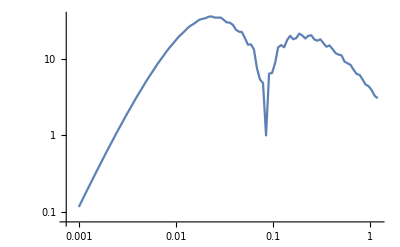

```mathematica
ListLogLogPlot[tabk // Abs, Joined -> True]
```

```mathematica
f2ker=integrandqμ[k,q,μ];
(* already contains the shape AND THE TWO FROM PERMUTATIONS! Just see the definition of II!!! The overall 1/2 in tabk, then, is from k𝒻/2... *)
Sker=𝒮[q,k,k-q]/.{mag[q]->q,mag[k]->k,mag[k-q]->√(k^2+q^2-2μ k q)}//FullSimplify;
```

```mathematica
direct=Monitor[Table[{k,NGparam/2×k×pℳ[k]NIntegrate[q^2(2π)/(2π)^3 (*2*)f2ker (*Sker*) pℳ[q]pℳ[√(k^2+q^2-2k q μ)],{q,0.0001,50},{μ,-1,1}]},{k,0.001,1.2,0.0025}],k]//Quiet;
```

```mathematica
(* careful that I account for the 1/2, and k!!! *)
```

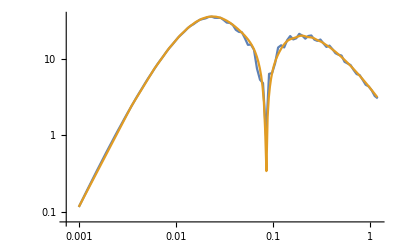

```mathematica
ListLogLogPlot[{tabk//Abs,Abs[direct]},Joined->True]
```

```mathematica
f=Interpolation[tabk//Re];
```

```mathematica
Export[NotebookDirectory[]<>"brute_force_points_b1f.m",direct];
```